```mathematica
NotebookEvaluate["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/00_SplinePack-034.nb"]  // Quiet;

Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/TP_ImProc_01-m101.wl"]] //Quiet;

Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/TP_ImProc_01-m101.wl"]] //Quiet;



Clear[SavitzkyGolayFilterExtended]


SavitzkyGolayFilterExtended[DOrder_,M_,nl_,nr_,data_] := Module[{i,j,p,t},
p = Table[t^i,{i,0,M}];
j = nl+nr+1;
i = Range[j];
Join[
D[Fit[Transpose[{i,Take[data,   j]}],p,t],{t,DOrder}]/.t->Take[i,  nl],
SavitzkyGolayFilter[DOrder,M,nl,nr,data],
D[Fit[Transpose[{i,Take[data,-j]}],p,t],{t,DOrder}]/.t->Take[i,-nr]]];



Clear[
ParamPadToTake,
ParamTakeToPad]


ParamPadToTake[ImgDim_,LeftRightBottomTop_] := {
{LeftRightBottomTop[[2,2]]+1,If[ListQ[ImgDim],ImgDim[[2]],-1]-LeftRightBottomTop[[2,1]]},
{LeftRightBottomTop[[1,1]]+1,If[ListQ[ImgDim],ImgDim[[1]],-1]-LeftRightBottomTop[[1,2]]}};


ParamTakeToPad[ImgDim_,RowsCols_] := Module[{LeftRightBottomTop},
LeftRightBottomTop = Reverse[RowsCols];
LeftRightBottomTop = Transpose[LeftRightBottomTop];
LeftRightBottomTop[[1]] -= 1;
LeftRightBottomTop[[2]] = ImgDim-LeftRightBottomTop[[2]];
LeftRightBottomTop = Transpose[LeftRightBottomTop];
LeftRightBottomTop[[2]] = Reverse[LeftRightBottomTop[[2]]];
LeftRightBottomTop];



Clear[
LoadFromTIF,
SaveAsTIF]


LoadFromTIF[CheckBitLength_,fname_] := Module[{X},
X = Import[fname];
X[[-1]] = ReadQRCode[X[[-1]]];
If[
If[TrueQ[CheckBitLength],
SameQ[
Piecewise[{{1,#≤1},{8,1<#≤8}},16]&/@Ceiling[Log[2,X[[-1,1]]]],
Ceiling[Log[2,Map[Length[Union@@ImageData[#]]&,Drop[X,-1]]]]],
True],
X[[-1]] = X[[-1,2]];
Fold[
ReplacePart[#1,#2[[1]],#2[[2]]]&,
X[[-1]],
Transpose[
{Drop[X,-1],
Position[X[[-1]],Image]}]]]];


SaveAsTIF[fname_,data_] := Module[{x,X},
X = data/.x_:>MyVectorPlaceholder/;ImageQ[x];
X = Append[
Extract[data,Position[X,MyVectorPlaceholder]],
X/.MyVectorPlaceholder->Image];
X[[-1]] = {Map[Length[Union@@ImageData[#]]&,Drop[X,-1]],X[[-1]]};
X[[-1]] = WriteQRCode[X[[-1]]];
MDExport[fname,X,"ImageEncoding"->"LZW"]];



Clear[ChangeImgDims]


ChangeImgDims[
  B_?ImageQ,
nx_?IntegerQ,
ny_?IntegerQ,
padding_] := Module[{R,x,y},
{x,y} = {nx,ny}-ImageDimensions[R=B];
If[y<0,
y = {Quotient[-y,2],-y};
y = {First[y],Subtract@@y}+{1,-1};
R = ImageTake[R,y],
If[y>0,
y = {y,Quotient[y,2]};
y = {Last[y],Subtract@@y};
R = ImagePad[R,{{0,0},y},padding]]];
If[x<0,
x = {Quotient[-x,2],-x};
x = {First[x],Subtract@@x}+{1,-1};
R = ImageTake[R,All,x],
If[x>0,
x = {x,Quotient[x,2]};
x = {Last[x],Subtract@@x};
R = ImagePad[R,{x,{0,0}},padding]]];
R];
```

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

```mathematica
$HistoryLength = 10;
```

```mathematica
PrependTo[MyTS,FontSize->24];
```

```mathematica
Clear[ToEnglish,Z]
```

```mathematica
DatenOrdner=OutPath = NotebookDirectory[]~~"output directory\\";
```

```mathematica
{ToEnglish,Z} = Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/EmissionRatePlotData.dat"]];
```

```mathematica
TableForm[Z]
Length[Z]
```

Proband | Instrument | Task | Begin (s) | End (s) | Emission rate (P/s) | ER σ (P/s) | Water emission (mg/s) | Particles/Water (P/mg)
 |  |  |  |  |  |  |  | 
C2 | C | Breathing | 6206 | 7408 | -98 | 171 | 6.35133 | -15.4298
C2 | C | Playing | 1200 | 2408 | 355 | 261 | 19.6555 | 18.0611
C2 | C | Playing With Surgical Mask | 8449 | 9061 | 790 | 764 | 7.36465 | 107.269
C2 | C | Speaking | 4010 | 5236 | 22 | 100 | 8.70055 | 2.52858
S1 | S | Breathing | 3340 | 4555 | 228 | 153 |  | 
S1 | S | Speaking | 1200 | 2405 | 89 | 94 |  | 
S1 | S | Speaking With Surgical Mask | 5466 | 6682 | -122 | 196 |  | 
S2 | S | Speaking With Surgical Mask | 4524 | 5723 | -1 | 184 | 4.8826 | -0.204809
S3 | S | Breathing | 4051 | 5256 | -157 | 302 | 8.03068 | -19.55
S3 | S | Speaking | 7443 | 8659 | 590 | 162 | 5.92732 | 99.5391
S3 | S | Speaking With Surgical Mask | 1200 | 2408 | 666 | 215 | 5.7454 | 115.919
S4 | S | Speaking | 5299 | 6523 | -137 | 198 | 5.18286 | -26.4333
S4 | S | Speaking With Surgical Mask | 424 | 1648 | 78 | 93 | 6.08984 | 12.8082
S5 | S | Speaking With Surgical Mask | 876 | 2098 | -50 | 107 | 5.95228 | -8.40014
S6 | S | Breathing | 4106 | 5320 | -199 | 335 | 8.3125 | -23.9398
S6 | S | Speaking | 1869 | 3080 | 16 | 189 | 17.5803 | 0.910107
S6 | S | Speaking With Surgical Mask | 6825 | 8040 | 114 | 267 | 5.6046 | 20.3404
S7 | S | Breathing | 3261 | 4466 | -105 | 151 | 3.11025 | -33.7593
S7 | S | Speaking | 5840 | 7058 | -260 | 312 | 5.79921 | -44.8337
S7 | S | Speaking With Surgical Mask | 1200 | 2405 | 473 | 83 | 6.94787 | 68.0784
S8 | S | Breathing | 3646 | 4851 | 48 | 164 | 3.95646 | 12.1321
S8 | S | Speaking | 7694 | 8906 | 203 | 327 | 4.58863 | 44.2398
S8 | S | Speaking With Surgical Mask | 1200 | 2440 | -163 | 249 | 9.10583 | -17.9006
S9 | S | Breathing | 3656 | 4859 | 455 | 302 | 8.05346 | 56.4975
S9 | S | Speaking | 7093 | 8303 | 1605 | 305 | 8.3908 | 191.281
S9 | S | Speaking With Surgical Mask | 1200 | 2403 | 586 | 610 | 10.1777 | 57.5767
S10 | S | Breathing | 4239 | 5441 | 296 | 224 | 8.28801 | 35.7142
S10 | S | Playing | 10644 | 11848 | 2122 | 605 | 12.8713 | 164.863
S10 | S | Speaking | 7057 | 8273 | 242 | 209 | 8.4451 | 28.6557
S10 | S | Speaking With Surgical Mask | 1200 | 2408 | 947 | 475 | 18.7504 | 50.5057
S11 | S | Breathing | 3418 | 4622 | 559 | 443 | 9.5607 | 58.4685
S11 | S | Speaking | 5828 | 7040 | 1671 | 207 | 9.96255 | 167.728
S11 | S | Speaking With Surgical Mask | 944 | 2159 | 2 | 413 | 9.34569 | 0.214002
S12 | S | Breathing | 4027 | 5230 | -44 | 210 | 12.5258 | -3.51274
S12 | S | Playing | 10374 | 11579 | 1355 | 428 | 16.1923 | 83.682
S12 | S | Speaking | 7275 | 8480 | 481 | 229 | 8.78184 | 54.7721
S12 | S | Speaking With Surgical Mask | 1093 | 2317 | 970 | 160 | 16.4966 | 58.8001
O2 | O | Breathing | 6157 | 7360 | -48 | 198 | 5.04529 | -9.51383
O2 | O | Playing | 1828 | 3032 | 838 | 288 | 19.4271 | 43.1356
O2 | O | Playing With Surgical Mask | 8546 | 9159 | 320 | 568 | 8.02528 | 39.874
O2 | O | Speaking | 4113 | 5328 | -245 | 356 | 8.90999 | -27.4972
O3 | O | Breathing | 5900 | 7104 | 23 | 166 | 5.18188 | 4.43854
O3 | O | Playing | 1200 | 2400 | 466 | 115 | 21.9253 | 21.254
O3 | O | Playing With Surgical Mask | 8292 | 8912 | 215 | 400 | 9.70404 | 22.1557
O3 | O | Speaking | 3515 | 4735 | 56 | 307 | 8.71046 | 6.42905
O3 | O | Speaking With Surgical Mask | 10570 | 11789 | -164 | 273 | 4.28641 | -38.2605
O4 | O | Breathing | 6226 | 7429 | 93 | 95 | 5.80198 | 16.029
O4 | O | Playing | 1200 | 2427 | 1309 | 210 | 16.382 | 79.9047
O4 | O | Playing With Surgical Mask | 8482 | 9086 | 911 | 612 | 6.44717 | 141.302
O4 | O | Speaking | 3697 | 4929 | 189 | 114 | 6.88974 | 27.4321
O4 | O | Speaking With Surgical Mask | 10224 | 11456 | -66 | 142 | 4.88131 | -13.521
O5 | O | Speaking | 3109 | 4303 | -164 | 319 | 11.3842 | -14.4059
O6 | O | Breathing | 6070 | 7281 | 117 | 304 | 9.31335 | 12.5626
O6 | O | Playing | 1200 | 2429 | 521 | 316 | 35.627 | 14.6238
O6 | O | Playing With Surgical Mask | 8842 | 9451 | 1610 | 483 | 9.25584 | 173.944
O6 | O | Speaking | 3683 | 4905 | 257 | 227 | 14.3611 | 17.8955
O7 | O | Breathing | 6229 | 7432 | 181 | 223 | 9.50645 | 19.0397
O7 | O | Playing | 1200 | 2433 | 2535 | 195 | 34.9787 | 72.4727
O7 | O | Playing With Surgical Mask | 8409 | 9017 | 670 | 238 | 13.4193 | 49.9282
O7 | O | Speaking | 3689 | 4894 | 715 | 296 | 18.8318 | 37.9676
O8 | O | Breathing | 7834 | 9039 | -187 | 432 | 7.19722 | -25.9823
O8 | O | Playing | 1569 | 2777 | 1229 | 147 | 32.4661 | 37.8549
O8 | O | Playing With Surgical Mask | 10204 | 10835 | 1053 | 273 | 15.7934 | 66.6734
O8 | O | Speaking | 5280 | 6512 | -175 | 294 | 9.94692 | -17.5934
O9 | O | Breathing | 6075 | 7278 | -145 | 266 | 5.34168 | -27.145
O9 | O | Playing | 1200 | 2404 | 1645 | 461 | 22.9649 | 71.6312
O9 | O | Playing With Surgical Mask | 8431 | 9042 | 1589 | 534 | 14.8384 | 107.087
O9 | O | Speaking | 4015 | 5222 | 9 | 191 | 7.94626 | 1.13261
O10 | O | Playing | 1200 | 2402 | 218 | 185 | 17.797 | 12.2493
O10 | O | Playing With Surgical Mask | 8608 | 9211 | -209 | 268 | 17.5343 | -11.9195
O10 | O | Speaking | 3747 | 4961 | -3 | 148 | 11.8492 | -0.253182
O10 | O | Speaking With Surgical Mask | 10242 | 11447 | -136 | 279 | 10.1543 | -13.3933
O11 | O | Breathing | 5645 | 6848 | 21 | 244 | 7.20408 | 2.91501
O11 | O | Playing | 1032 | 2258 | 1484 | 211 | 26.5107 | 55.9774
O11 | O | Playing With Surgical Mask | 8124 | 8741 | 1263 | 1224 | 10.8125 | 116.809
O11 | O | Speaking | 3379 | 4595 | 144 | 409 | 13.1723 | 10.932
O12 | O | Breathing | 6274 | 7483 | -150 | 196 | 8.32992 | -18.0074
O12 | O | Playing | 1200 | 2411 | 660 | 274 | 24.5285 | 26.9075
O12 | O | Playing With Surgical Mask | 8782 | 9386 | 894 | 620 | 14.5733 | 61.3453
O12 | O | Speaking | 3565 | 4770 | 725 | 128 | 12.7055 | 57.0621
F1 | F | Breathing | 5183 | 6376 | 48 | 35 | 6.17609 | 7.7719
F1 | F | Playing | 1200 | 2392 | 1434 | 366 | 26.468 | 54.1787
F1 | F | Speaking | 3057 | 4260 | 641 | 384 | 11.7497 | 54.5544
F1 | F | Speaking With Surgical Mask | 6929 | 8125 | 447 | 189 | 8.23895 | 54.2545
F2 | F | Breathing | 6063 | 7278 | 119 | 151 | 7.49066 | 15.8865
F2 | F | Playing | 1379 | 2586 | 343 | 486 | 29.3035 | 11.7051
F2 | F | Speaking | 3612 | 4826 | 63 | 92 | 14.9865 | 4.20379
F3 | F | Breathing | 3293 | 4493 | 39 | 213 |  | 
F3 | F | Playing | 1588 | 2755 | 57 | 175 |  | 
F3 | F | Speaking | 4983 | 6228 | -144 | 175 |  | 
F3 | F | Speaking With Surgical Mask | 7425 | 8615 | 455 | 293 |  | 
F4 | F | Breathing | 5604 | 6813 | -2 | 317 | 8.18271 | -0.244418
F4 | F | Playing | 1200 | 2405 | 2318 | 644 | 27.4037 | 84.587
F4 | F | Speaking | 3543 | 4759 | -79 | 366 | 13.6893 | -5.77093
F4 | F | Speaking With Surgical Mask | 7928 | 9141 | 432 | 245 | 6.09656 | 70.8597
F5 | F | Playing | 1200 | 2401 | 1143 | 206 | 21.095 | 54.1834
F5 | F | Speaking | 4001 | 5223 | -80 | 174 | 6.67978 | -11.9764
F5 | F | Speaking With Surgical Mask | 8298 | 9499 | -89 | 291 | 5.70864 | -15.5904
F6 | F | Breathing | 4996 | 6211 | 350 | 175 | 12.8319 | 27.2759
F6 | F | Playing | 1200 | 2416 | 635 | 128 |  | 
F6 | F | Speaking | 3159 | 4364 | 7 | 67 | 23.5479 | 0.297266
F7 | F | Breathing | 5401 | 6604 | -1 | 79 |  | 
F7 | F | Playing | 1200 | 2420 | 1171 | 176 |  | 
F7 | F | Speaking | 3399 | 4611 | 129 | 256 |  | 
F7 | F | Speaking With Surgical Mask | 7200 | 8407 | 486 | 220 |  | 
F9 | F | Breathing | 5911 | 7119 | 274 | 317 | 4.31308 | 63.5277
F9 | F | Playing | 1200 | 2404 | 799 | 307 | 8.14177 | 98.1359
F9 | F | Speaking | 3521 | 4759 | -121 | 140 | 5.55579 | -21.7791
F9 | F | Speaking With Surgical Mask | 8075 | 9283 | 474 | 368 | 5.38106 | 88.0868
F10 | F | Playing | 1200 | 2398 | 11 | 288 |  | 
F10 | F | Speaking | 3145 | 4340 | 5 | 203 | 18.3802 | 0.272032
F10 | F | Speaking With Surgical Mask | 6889 | 8093 | 943 | 173 | 5.75107 | 163.97
F11 | F | Breathing | 5914 | 7118 | 149 | 368 | 3.98727 | 37.3689
F11 | F | Playing | 1200 | 2413 | 15 | 313 | 18.7977 | 0.797972
F12 | F | Breathing | 5897 | 7103 | -127 | 237 | 6.85545 | -18.5254
F12 | F | Playing | 1160 | 2375 | 1708 | 348 | 29.6123 | 57.6787
F12 | F | Speaking | 3754 | 4965 | 251 | 163 | 10.3012 | 24.3661
F12 | F | Speaking With Surgical Mask | 8233 | 9443 | 564 | 295 | 6.65816 | 84.7081
F13 | F | Playing | 1095 | 2307 | 905 | 75 | 12.3282 | 73.409
F13 | F | Speaking | 3354 | 4557 | 228 | 191 | 9.82398 | 23.2085
F13 | F | Speaking With Surgical Mask | 8378 | 9576 | 88 | 239 | 5.65073 | 15.5732
F14 | F | Breathing | 6529 | 7740 | 181 | 209 | 3.6099 | 50.14
F14 | F | Playing | 1200 | 2425 | 700 | 368 | 13.7627 | 50.862
F14 | F | Speaking | 3939 | 5168 | 64 | 253 | 7.93103 | 8.06957
F15 | F | Breathing | 6108 | 7316 | -11 | 196 | 4.08124 | -2.69526
F15 | F | Playing | 1200 | 2404 | 2358 | 120 | 24.8061 | 95.0573
F15 | F | Speaking | 3849 | 5063 | 233 | 215 | 9.1381 | 25.4976
F15 | F | Speaking With Surgical Mask | 8331 | 9540 | 31 | 316 | 4.55566 | 6.80472
F16 | F | Breathing | 6620 | 7824 | 200 | 83 | 6.77415 | 29.524
F16 | F | Playing | 1200 | 2409 | 364 | 278 | 33.7478 | 10.7859
F16 | F | Speaking | 4532 | 5738 | 298 | 187 | 12.2373 | 24.3518
F17 | F | Breathing | 6635 | 7852 | 21 | 124 | 3.95503 | 5.3097
F17 | F | Playing | 1200 | 2418 | 512 | 294 | 17.1398 | 29.872
F17 | F | Speaking | 4614 | 5820 | 410 | 161 | 6.47669 | 63.3039
F17 | F | Speaking With Surgical Mask | 9133 | 10355 | 1125 | 161 | 4.30338 | 261.423
F18 | F | Breathing | 6927 | 8129 | 86 | 191 | 5.96245 | 14.4236
F18 | F | Playing | 1516 | 2727 | 390 | 155 | 19.7321 | 19.7648
F18 | F | Speaking | 4058 | 5259 | 427 | 123 | 11.2176 | 38.0651
F18 | F | Speaking With Surgical Mask | 9464 | 10668 | 513 | 395 | 8.31043 | 61.7296
F19 | F | Breathing | 6116 | 7321 | 589 | 354 | 5.46943 | 107.689
F19 | F | Playing | 1200 | 2423 | 1917 | 365 | 8.88526 | 215.751
F19 | F | Speaking | 3664 | 4888 | 681 | 151 | 2.84054 | 239.743
F19 | F | Speaking With Surgical Mask | 9035 | 10245 | 776 | 531 | 3.76071 | 206.344
F20 | F | Breathing | 6432 | 7665 | 204 | 140 | 3.8381 | 53.1514
F20 | F | Playing | 1200 | 2403 | 1410 | 342 | 13.9815 | 100.848
F20 | F | Speaking | 3807 | 5022 | 770 | 152 | 5.98523 | 128.65
F20 | F | Speaking With Surgical Mask | 8636 | 9874 | 559 | 162 | 5.27915 | 105.888
T1 | T | Playing | 1200 | 2415 | 192 | 448 | 30.0835 | 6.38223
T1 | T | Playing With Surgical Mask | 8984 | 9589 | 28 | 2562 | 9.06738 | 3.08799
T1 | T | Speaking | 3907 | 5135 | -306 | 348 | 13.4608 | -22.7327

152

```mathematica
Entries[Z,"Instrument"]
```

{{67,F},{43,O},{33,S},{4,C},{3,T}}

```mathematica
Entries[Z,"Aufgabe"/.ToEnglish]
```

{{41,Speaking},{35,Breathing},{33,Playing},{29,Speaking With Surgical Mask},{12,Playing With Surgical Mask}}

```mathematica
Measurements = {"Atmen","Sprechen mit MNS","Sprechen","Musikspiel mit Schutz","Musikspiel"}/.ToEnglish;
TableForm[Subsets[Measurements,{2}]]
```

Breathing | Speaking With Surgical Mask
Breathing | Speaking
Breathing | Playing With Surgical Mask
Breathing | Playing
Speaking With Surgical Mask | Speaking
Speaking With Surgical Mask | Playing With Surgical Mask
Speaking With Surgical Mask | Playing
Speaking | Playing With Surgical Mask
Speaking | Playing
Playing With Surgical Mask | Playing

```mathematica
Clear[R,CorrPlotWater,
A,a,c,g,p,s,x,α]

R = 40;

CorrPlotWater[
instr_?StringQ,
        X_?StringQ,
        Y_?StringQ] := Module[{A,a,c,g,p,s,x,α},
A = SelectRows[Z,"Instrument"/.ToEnglish,(#==(instr/.ToEnglish))&];
If[a=(Length[A]==2),A = Z];
A = {
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(X/.ToEnglish))&],
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(Y/.ToEnglish))&]};
If[Min[Length/@A]==2,Return[2]];
A = Map[Drop[ExtractColumn[#,{"Proband","Wasseremission (mg/s)"}/.ToEnglish],2]&,A];
A = Map[Select[#,NumericQ[#[[2]]]&]&,A];
If[Min[Length/@A]==0,Return[3]];
A = MyMerge[A[[1]],A[[2]],1,True];
If[A=={},Return[4]];
p = Map[StringDrop[#,1]&,First/@A];
p = SortBy[p,ToExpression];
p = ConcatStringList[p,", "];
p = StringJoin[p,"  (n = ",ToString[Length[A]],")"];
A = Last/@A;
A = Transpose/@A;
A = Flatten[A,1];
g = Map[({Cos[α],Sin[α]}.#)&,A];
g = NMinimize[g.g,α];
g = α/.g[[2]];
g = Tan[g+π/2];

{x,y} = Transpose[A];
x -= Mean[x];
y -= Mean[y];
Print["r = "<>ToString[(x.y)/Sqrt[x.x*y.y]]];

A = Point[A];
c = Y/.{
"Atmen"                                       ->Hue[2/3,0.6,1],
"Sprechen mit MNS"              ->Hue[1/3,0.4,0.9],
"Sprechen"                                ->Hue[1/3,1.0,0.8],
"Musikspiel mit Schutz"  ->Hue[0/3,0.4,1],
"Musikspiel"                           ->Hue[0/3,1.0,1],
"Luftreiniger"                       ->PatternFilling["Hexagon",ImageScaled[0.008]],
"Messbereich"                         ->GrayLevel[0.7],
"Proband im Messbereich"->GrayLevel[0.9],
"Ventilator"                           ->PatternFilling["Chevron",ImageScaled[0.005]]};
s = {
FontColor->GrayLevel[0.5],
FontFamily->"Arial",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->Round[(FontSize/.MyTS)*5/6]};
A = Graphics[
{Text[Style@@Prepend[s,If[a,"",p]                                                        ],Scaled[  0.98*{1,1}],{1,1}],
Text[Style@@Prepend[s,StringJoin["f = ",RealForm[g,4,2]]],Scaled[{0.98,0.94} ],{1,1}],
If[NumericQ[R],
{AbsoluteThickness[5],
GrayLevel[0.9],
Line[Transpose[{#,g*#}]&[
{0,0.93*R*Min[1,1/g]}]]},
Nothing],
AbsolutePointSize[20],c,A},
AspectRatio->If[R===All,1,Automatic],
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{
StringJoin["Water emission during ",ToLowerCase[X/.ToEnglish],",   mg/s"],
StringJoin["Water emission during ",ToLowerCase[Y/.ToEnglish],",   mg/s"]},
GridLines->Automatic,
ImageSize->1000,
LabelStyle->MyTS,
PlotLabel->instr/.{"Alle"->"All","Kl"->"Clarinet","KP"->"Singing","Ob"->"Oboe","Qu"->"Flute","Tr"->"Trumpet"},
PlotRange->{{0,R},{0,R}},
PlotRangeClipping->True];

Print[
MDExport[
StringJoin[OutPath,"Fig\\CorrPlots\\mg-s\\",instr,"~",Y,"(",X,")_Water.tif"],
Rasterize[A],
"ImageEncoding"->"LZW"]];

Print[A];
];

(*
CorrPlotWater["Qu","Sprechen","Musikspiel"];
*)
```

r = 0.899105

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\CorrPlots\mg-s

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\CorrPlots\mg-s\Qu~Atmen(Sprechen)_Water.tif

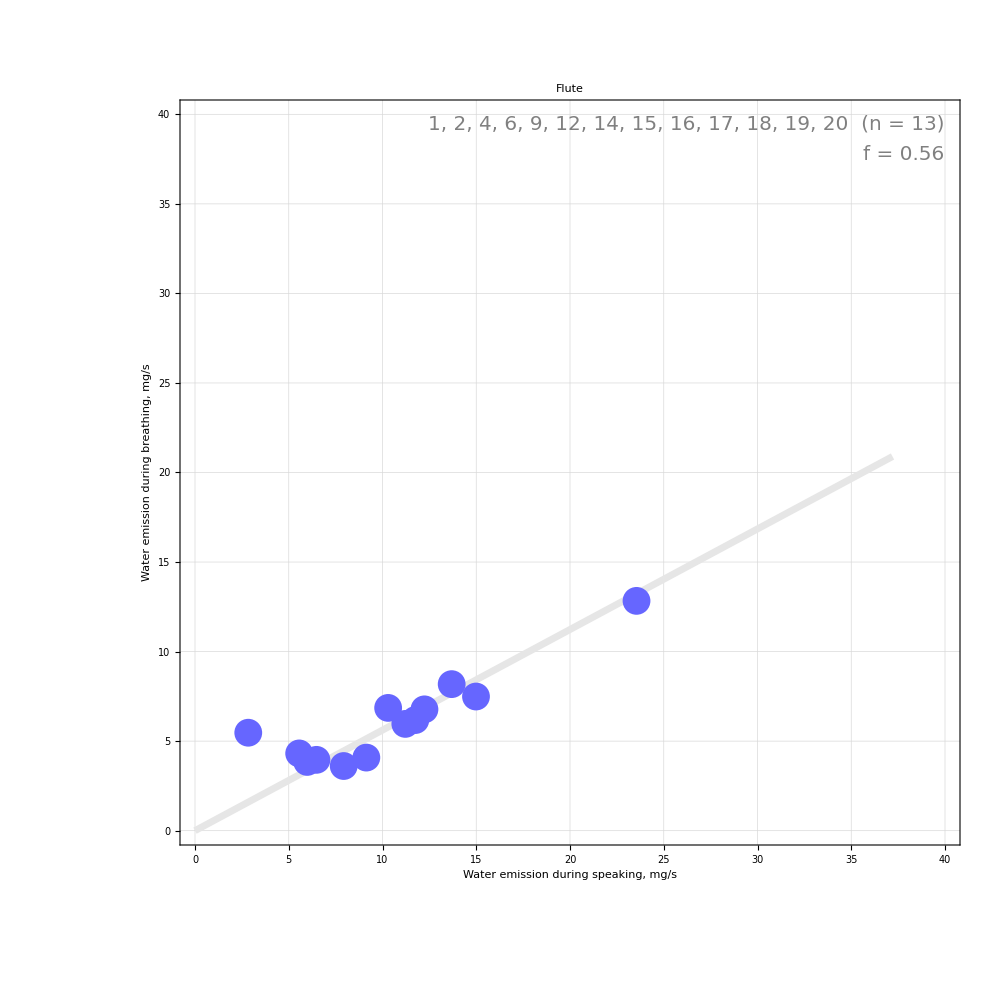

r = 0.519267

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\CorrPlots\mg-s\Qu~Sprechen mit MNS(Sprechen)_Water.tif

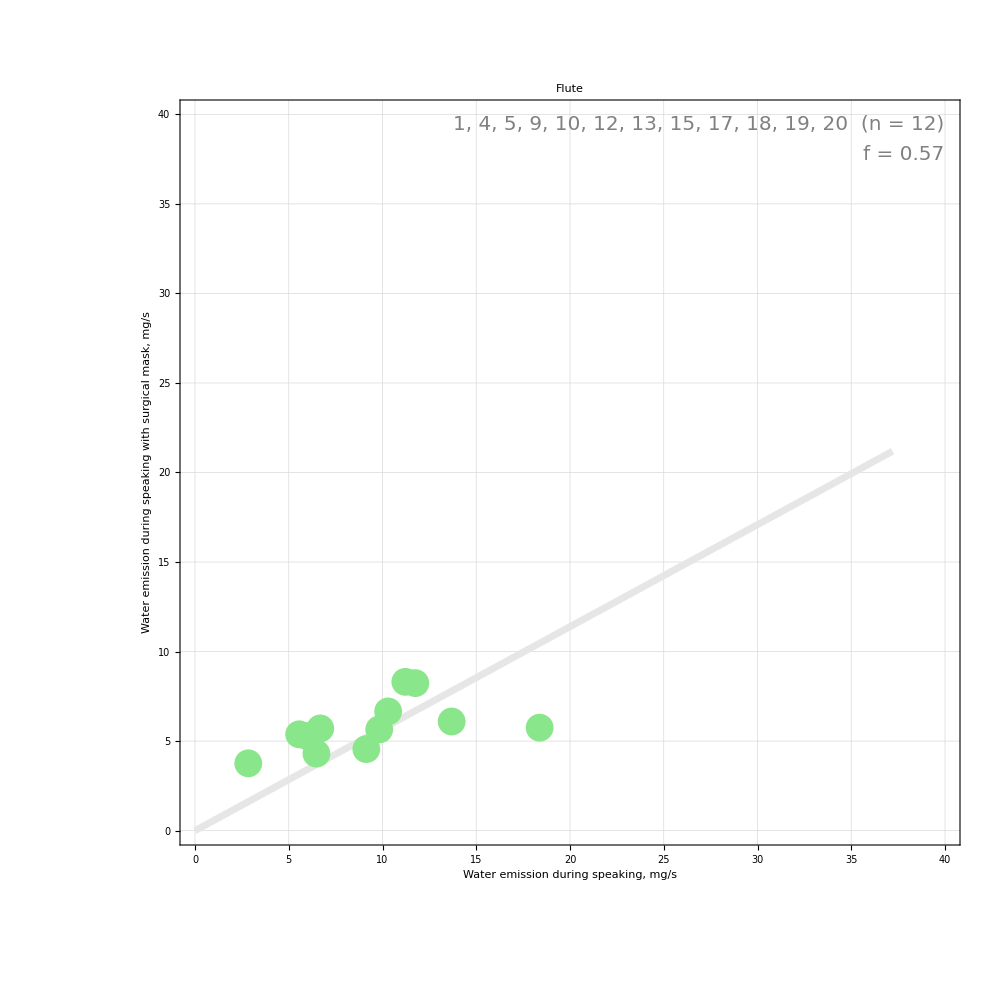

r = 0.798748

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\CorrPlots\mg-s\Qu~Musikspiel(Sprechen)_Water.tif

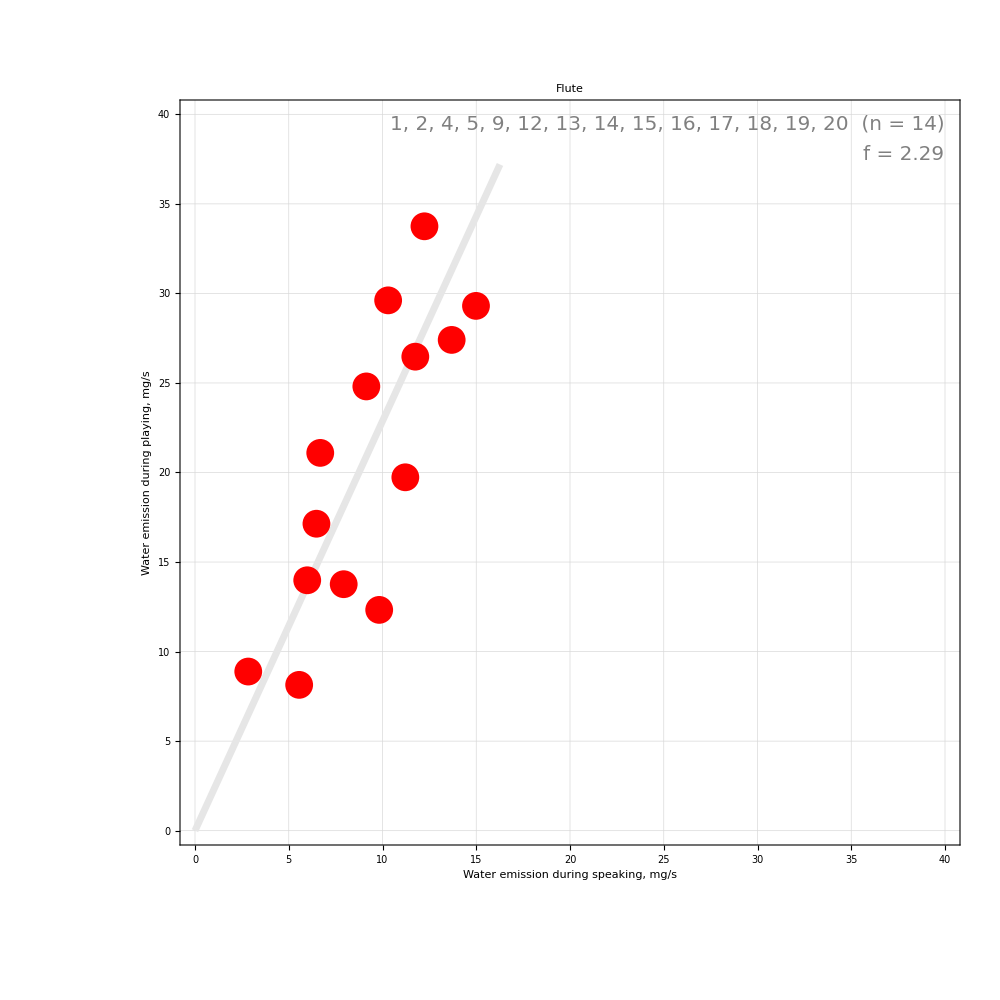

r = 0.699616

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\CorrPlots\mg-s\Qu~Musikspiel(Atmen)_Water.tif

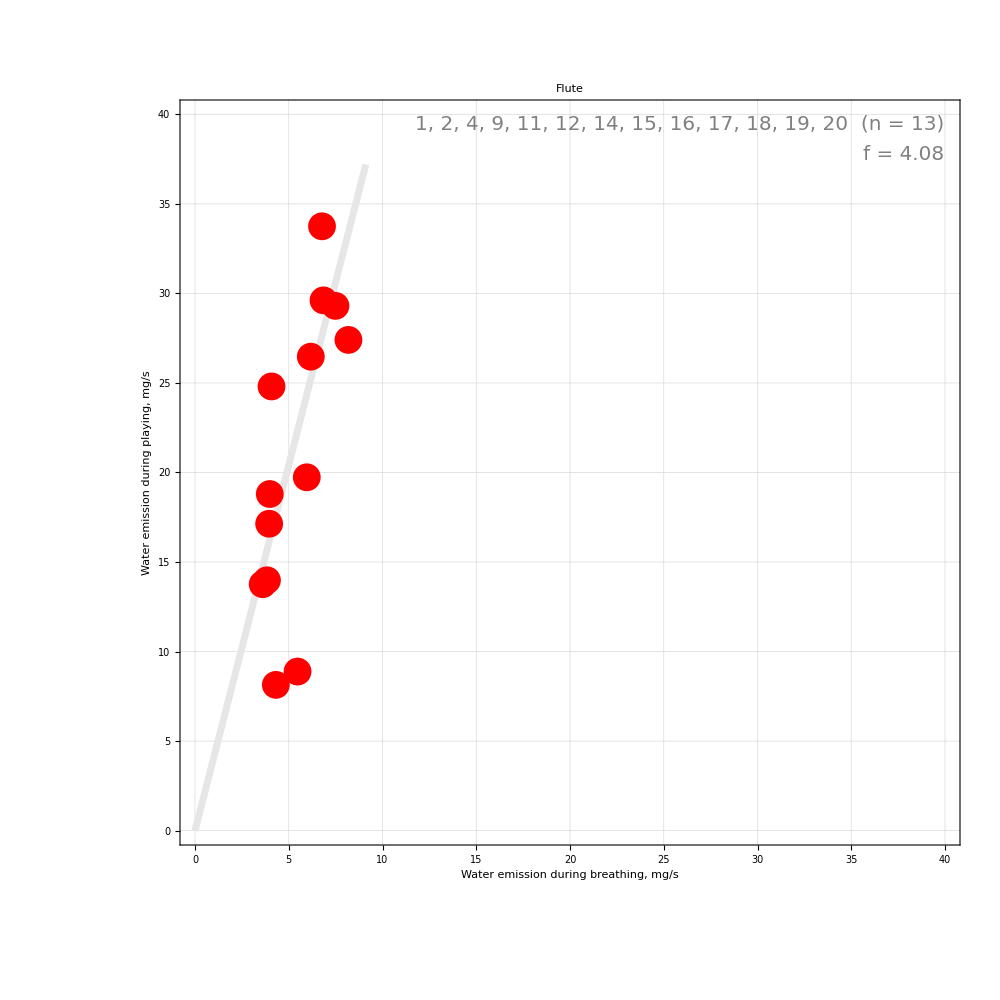

r = 0.896135

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\CorrPlots\mg-s\Ob~Atmen(Sprechen)_Water.tif

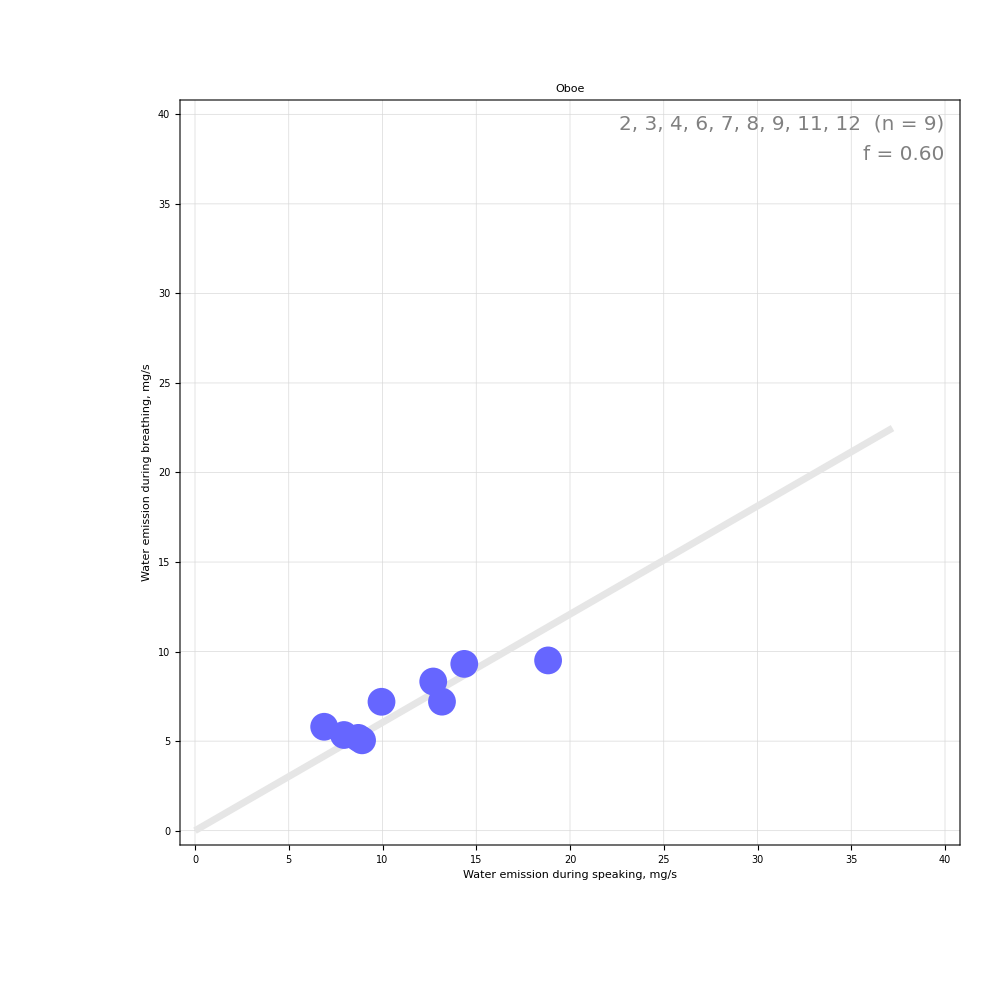

r = 0.894459

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\CorrPlots\mg-s\Ob~Sprechen mit MNS(Sprechen)_Water.tif

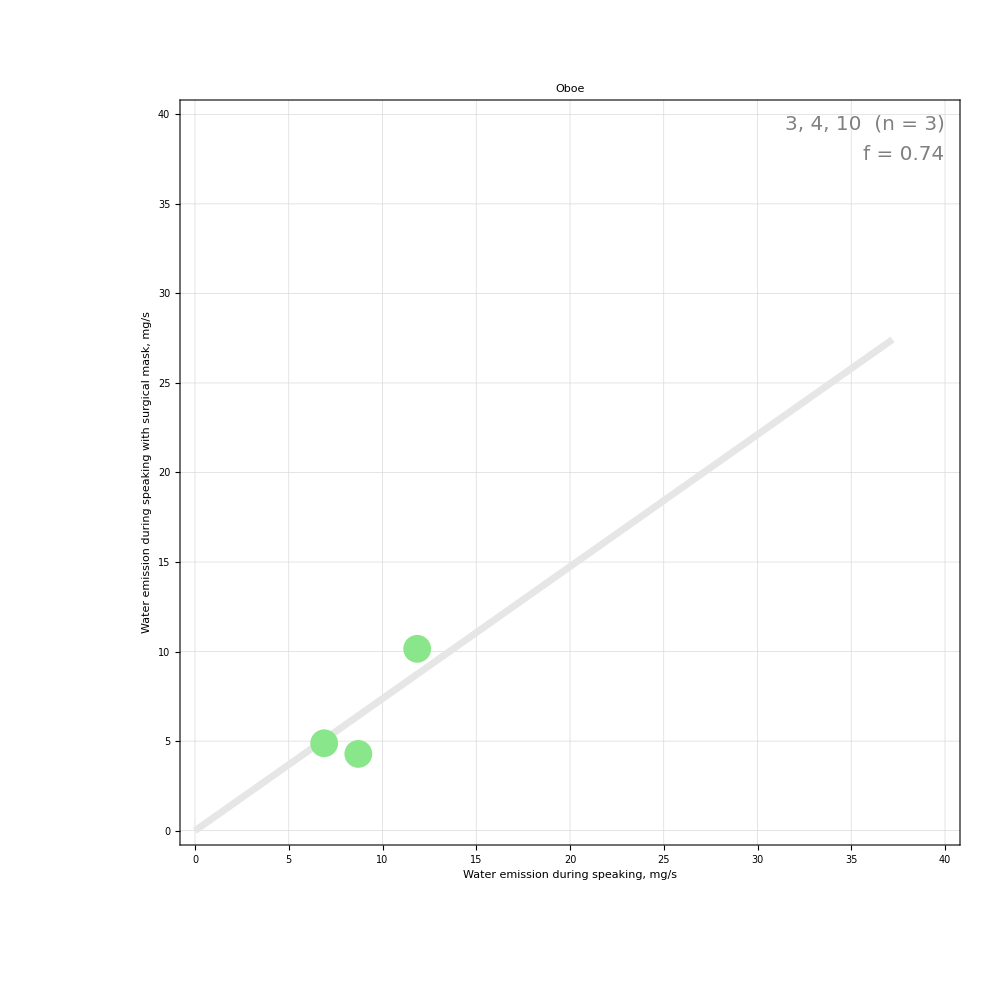

r = 0.713072

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\CorrPlots\mg-s\Ob~Musikspiel(Sprechen)_Water.tif

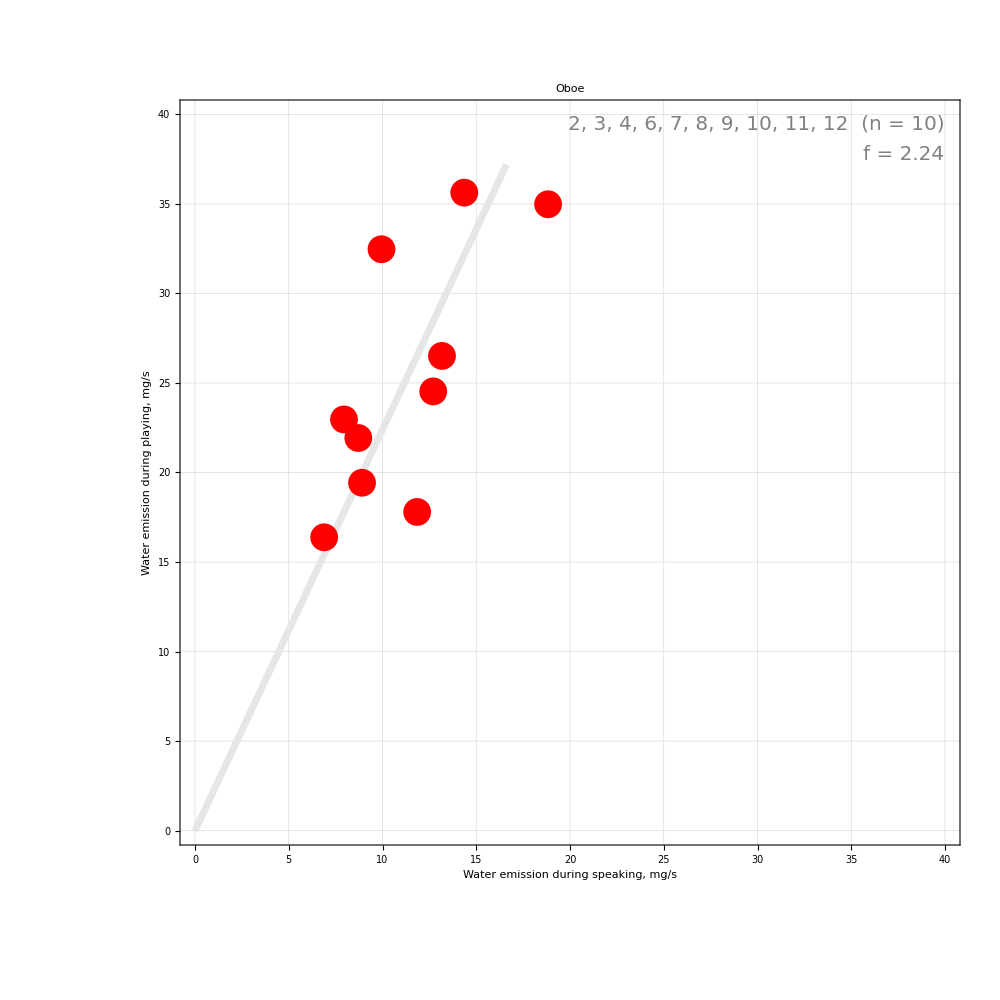

r = 0.835778

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\CorrPlots\mg-s\Ob~Musikspiel(Atmen)_Water.tif

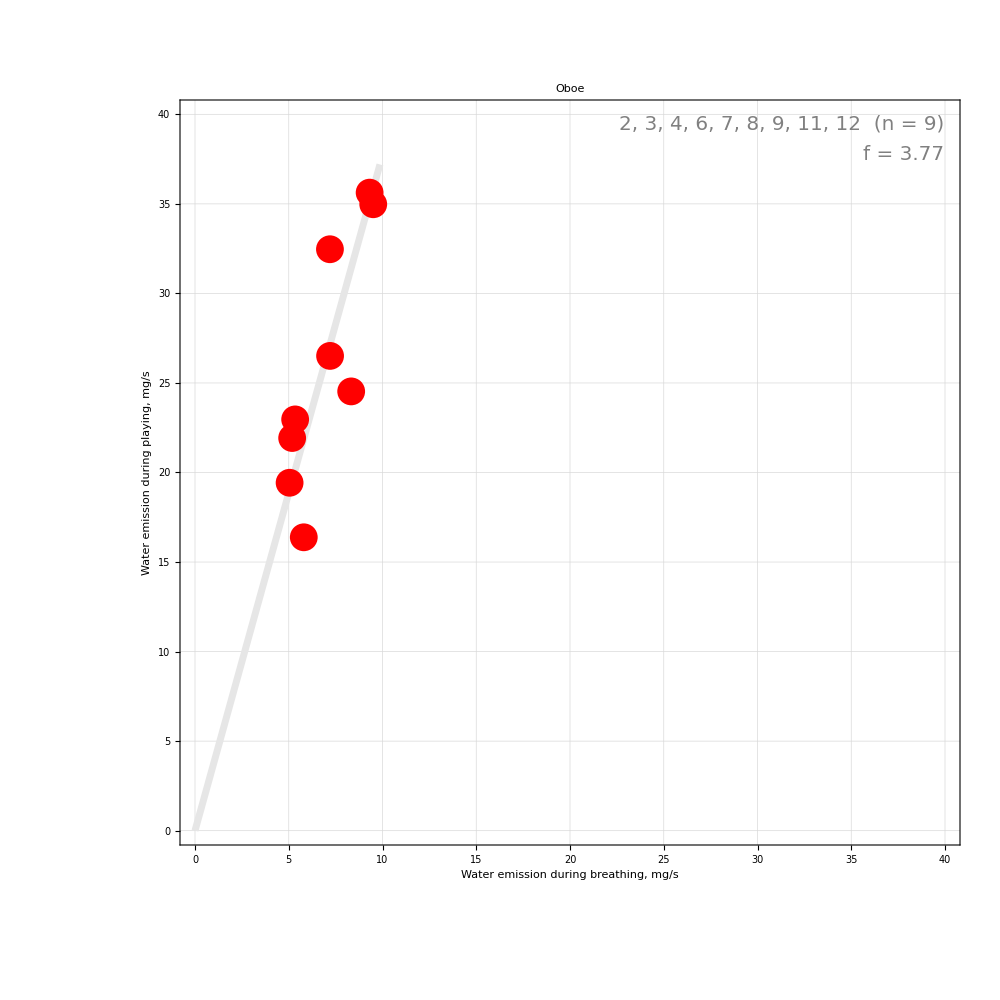

r = 0.179122

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\CorrPlots\mg-s\Ob~Musikspiel mit Schutz(Musikspiel)_Water.tif

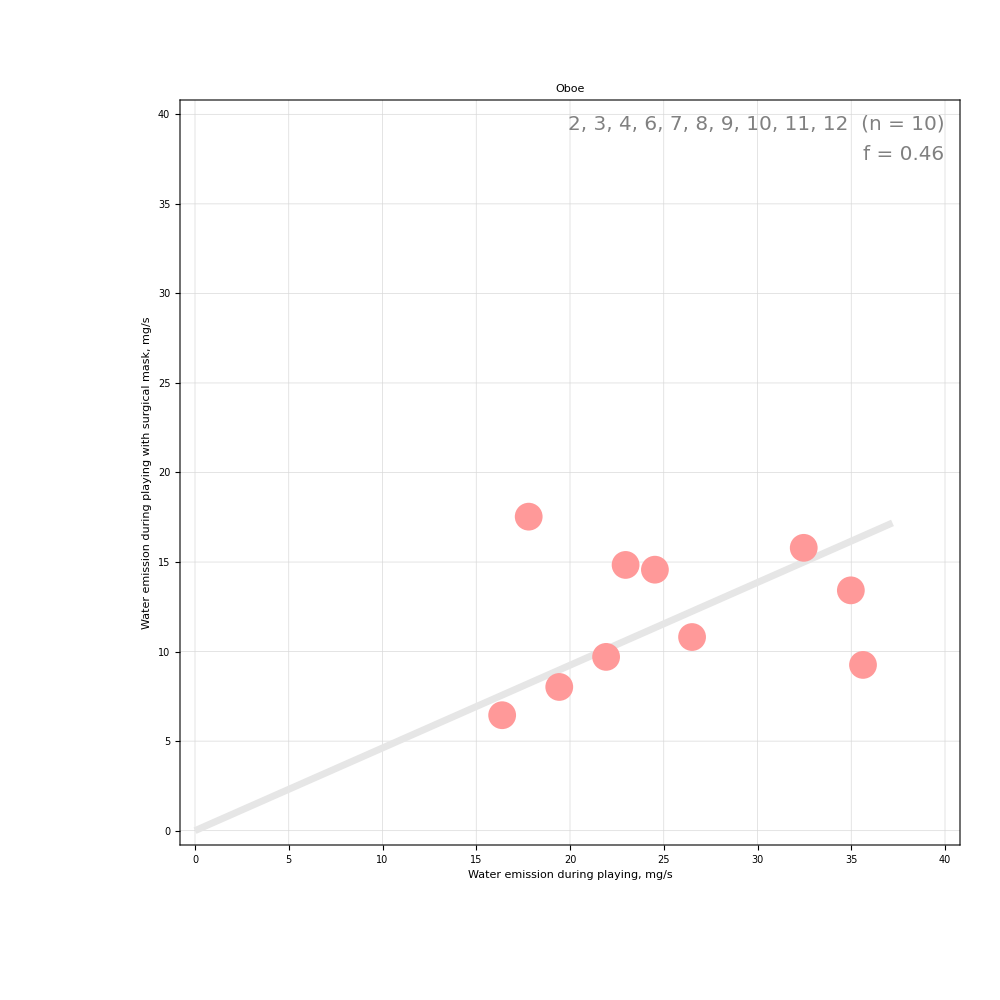

```mathematica
Scan[(
CorrPlotWater[#,"Sprechen","Atmen"];
CorrPlotWater[#,"Sprechen","Sprechen mit MNS"];
CorrPlotWater[#,"Sprechen","Musikspiel"];
CorrPlotWater[#,"Atmen"       ,"Musikspiel"];
CorrPlotWater[#,"Musikspiel","Musikspiel mit Schutz"]
)&,
{(*"Alle",*)"Qu","Ob"(*,"KP","Kl","Tr"*)}];
```

### output is online available https://github.com/Carl-Firle/my-data-storage/tree/main/data/2020_aerosol-wind-instruments/Fig/CorrPlots/mg-s